Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

3 - 5 Application of theorem 1

3.  Find the potential Φ in the region R in the first quadrant of the z-plane bounded by the axes (having potential U_1) and the hyperbola y = 1/x (having potential U_2) by mapping R onto a suitable infinite strip. Show that Φ is harmonic. What are its boundary values?

```mathematica
Clear["Global`*"]
```

The region plot is of an infinite region, and the 6 sample points are for trying to keep track of what maps where.

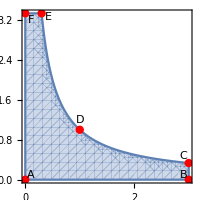

```mathematica
RegionPlot[0<y&&0<x&&y<1/x,{x,0,3},{y,0,10/3},ImageSize->200,Epilog->{{Red,PointSize[0.03],Point[{0,0}]},{Red,PointSize[0.03],Point[{3,0}]},{Red,PointSize[0.03],Point[{3,1/3}]},{Red,PointSize[0.03],Point[{1,1}]},{Red,PointSize[0.03],Point[{0.3,1/0.3}]},{Red,PointSize[0.03],Point[{0,10/3}]},{Text[Style[A,Medium],{0.1,0.1}]},{Text[Style[B,Medium],{2.9,0.1}]},{Text[Style[C,Medium],{2.9,0.48}]},{Text[Style[D,Medium],{1,1.2}]},{Text[Style["E",Medium],{0.42,3.25}]},{Text[Style[F,Medium],{0.1,3.2}]}}]
```

One useful way to set up what the text answer seems to refer to as t-space is to establish an ImplicitRegion.

```mathematica
d1=ImplicitRegion[0<x∧0<y∧y<1/x,{x,y}];
```

Then the implicit region can be mapped onto a semi-infinite strip using the squaring function. Having played with this before, I recognize that the squaring function by itself will give a horizontal strip (below right), or I could agree with the rotation contained in the text answer and throw in the ⅈ for a vertical strip (below left). Either way it is a semi-infinite strip, not an infinite one. First I will try it my way. Note that the domain of the mapping is taken directly off the implicit region.

(If I make an array of sample points and calculate them in advance it will save space.)

```mathematica
sx={{0,0},{3,0},{3,1/3},{1,1},{0.3,1/0.3},{0,10/3}}
```

{{0,0},{3,0},{3,1/3},{1,1},{0.3,3.33333},{0,10/3}}

Since the points are for plotting, I don’t need super high accuracy.

```mathematica
gp[{x_,y_}]={N[Re[(x+ⅈ y)^2]],N[Im[(x+ⅈ y)^2]]}
```

{Re[(x+(0.+1. ⅈ) y)^2],Im[(x+(0.+1. ⅈ) y)^2]}

```mathematica
Thread[gp[ sx]]
```

{{0.,0.},{9.,0.},{8.88889,2.},{0.,2.},{-11.0211,2.},{-11.1111,0.}}

Then a version of the points for the mapping according to the approach implied by the text answer.

```mathematica
tp[{x_,y_}]={N[Re[ⅈ(x+ⅈ y)^2]],N[Im[ⅈ(x+ⅈ y)^2]]}
```

{-1. Im[(x+(0.+1. ⅈ) y)^2],Re[(x+(0.+1. ⅈ) y)^2]}

```mathematica
Thread[tp[ sx]]
```

{{0.,0.},{0.,9.},{-2.,8.88889},{-2.,0.},{-2.,-11.0211},{0.,-11.1111}}

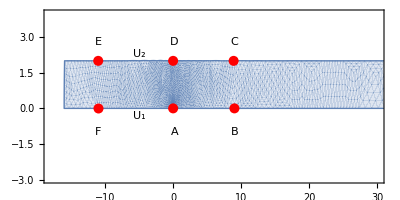
-Graphics--Graphics-

```mathematica
Row[{ParametricPlot[Through[{Re,Im}[ⅈ(x+ⅈ y)^2]],{x,y}∈d1, PlotRange->{{-10,10},{-20,120}},Frame->True,ImageSize->200,Epilog->{{Red,PointSize[0.05],Point[{0,0}]},{Text[Style[A,Medium],{1,-1.1}]},{Red,PointSize[0.05],Point[{0,9}]},{Text[Style[B,Medium],{1,9}]},{Red,PointSize[0.05],Point[{-2,8.9}]},{Text[Style[C,Medium],{-3.2,9}]},{Red,PointSize[0.05],Point[{-2,0}]},{Text[Style[D,Medium],{-3,-1.1}]},{Red,PointSize[0.05],Point[{-2,-11}]},{Text[Style["E",Medium],{-3,-11}]},{Red,PointSize[0.05],Point[{0,-11}]},{Text[Style[F,Medium],{1,-11.3}]},{Text[Style[ Subscript[U, 1],Medium],{1,-4.3}]},{Text[Style[ Subscript[U, 2],Medium],{-3,-4}]}}],ParametricPlot[Through[{Re,Im}[(x+ⅈ y)^2]],{x,y}∈d1, PlotRange->{{-18,30},{-3,4}},Frame->True,ImageSize->400,Epilog->{{Red,PointSize[0.018],Point[{0,0}]},{Text[Style[A,Medium],{0.2,-1}]},{Red,PointSize[0.018],Point[{9,0}]},{Text[Style[B,Medium],{9,-1}]},{Red,PointSize[0.018],Point[{8.88,2}]},{Text[Style[C,Medium],{9,2.8}]},{Red,PointSize[0.018],Point[{0,2}]},{Text[Style[D,Medium],{0.2,2.8}]},{Red,PointSize[0.018],Point[{-11,2}]},{Text[Style["E",Medium],{-11,2.8}]},{Red,PointSize[0.018],Point[{-11,0}]},{Text[Style[F,Medium],{-11,-1}]},{Text[Style[ Subscript[U, 1],Medium],{-5,-0.3}]},{Text[Style[ Subscript[U, 2],Medium],{-5,2.3}]}}]}]
```

Problem 17 in section 17.4 looks a lot like this, except the equation of the hyperbola is different. After doing some research, almost everything I found on line deals with double mapping, because a semi-infinite strip is evidently normally mapped to a half plane for analysis. Then there are three planes, z-plane, Z-plane, and w-plane. To model the w-plane, I need to access the array of once-mapped sample points.

```mathematica
ss={{0,0},{9,0},{80/9,2},{0,2},{-11.021111111111113,2.},{-100/9,0}}
```

{{0,0},{9,0},{80/9,2},{0,2},{-11.0211,2.},{-100/9,0}}

So I can re-map them.

```mathematica
gs2[{x_,y_}]={N[Re[Exp[x+π/2 ⅈ y]],2],N[Im[Exp[x+π/2 ⅈ y]],2]}
```

{Re[2.7^(x+(0.+1.6 ⅈ) y)],Im[2.7^(x+(0.+1.6 ⅈ) y)]}

```mathematica
Thread[gs2[ ss]]
```

{{1,0},{8000.,0},{-7000.,0``-2.518960637510923},{-1.,0.},{-0.0000163528,2.00264×10^-21},{0.00001,0}}

And now to map the semi-infinite strip to a half plane. In this case it happens to be horizontal. I don’t see an advantage to rotating it.

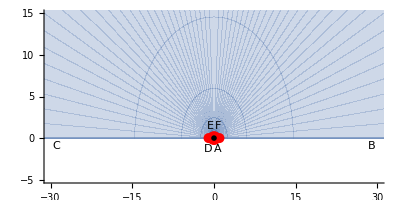

```mathematica
ParametricPlot[Through[{Re,Im}[Exp[x+π/2 ⅈ y]]],{x,-25,25},{y,0,2}, PlotRange->{{-30,30},{-5,15}},Frame->False,ImageSize->400,Epilog->{{Red,PointSize[0.018],Point[{1,0}]},{Text[Style[A,Medium],{0.7,-1.3}]},{Red,PointSize[0.018],Point[{8000,0}]},{Text[Style[B,Medium],{29,-1}]},{Red,PointSize[0.018],Point[{-7000,0}]},{Text[Style[C,Medium],{-29,-1}]},{Red,PointSize[0.018],Point[{-1,0}]},{Text[Style[D,Medium],{-1,-1.3}]},{Red,PointSize[0.025],Point[{0,0}]},{Text[Style["E",Medium],{-0.7,1.5}]},{Black,PointSize[0.01],Point[{0,0}]},{Text[Style[F,Medium],{0.7,1.5}]}}]
```

I see that the disposition of sample points is sort of problematic. Points B and C are off the plot. But right now, my focus is on groups of points. F, A, B, associated with potential U_1, can be interpreted as being on the right, and points C, D, E, associated with potential U_2, are on the left. And, noting that the semi-plane is infinite makes it seem like a natural for example 3 on p. 760, the potential of an angular sector, with the sector α=π.

This looks okay so far, but it is overly complicated with two successive mappings. The way to go would be a composition function that would do it all in one step. So, how about

```mathematica
girt[{x_,y_}]={Re[(x+ⅈ y)^2],Im[(x+ⅈ y)^2]}
```

{Re[(x+ⅈ y)^2],Im[(x+ⅈ y)^2]}

for the hyperbola-to-strip, and

```mathematica
toside[{x_,y_}]={Re[ⅇ^(x+(ⅈ π y)/2)],Im[ⅇ^(x+(ⅈ π y)/2)]}
```

{Re[ⅇ^(x+(ⅈ π y)/2)],Im[ⅇ^(x+(ⅈ π y)/2)]}

for the strip to semi-plane, the two rolled up into

```mathematica
combi[{x_,y_}]=Composition[toside,girt][{x,y}]
```

{Re[ⅇ^(1/2 ⅈ π Im[(x+ⅈ y)^2]+Re[(x+ⅈ y)^2])],Im[ⅇ^(1/2 ⅈ π Im[(x+ⅈ y)^2]+Re[(x+ⅈ y)^2])]}

The following test shows that the composition function handles all the sample points correctly.

```mathematica
N[Thread[combi[ sx]]]
```

{{1.,0.},{8103.08,0.},{-7250.96,0.},{-1.,0.},{-0.0000163528,2.00264×10^-21},{0.0000149453,0.}}

On the combi declaration out-line [xxx] I can see under the function’s hood to tell what it really is.

```mathematica
ⅇ^(1/2 ⅈ π z^2)
```

ⅇ^(1/2 ⅈ π z^2)

Expanding shows off some simple components

```mathematica
ComplexExpand[%]
```

Cos[(π z^2)/2]+ⅈ Sin[(π z^2)/2]

Bringing in the punchline of example 3 on p. 760. (Note: the v/u instead of y/x below was Murray Spiegel’s idea.) Doing some reorganizing, and subject as always to my mistakes,

```mathematica
Φ[x,y]=1/2(Subscript[Φ, 2]+Subscript[Φ, 1])+1/π(Subscript[Φ, 1]-Subscript[Φ, 2])ArcTan[v/u] ⟹
```

```mathematica
Φ[x,y]=1/2(Subscript[Φ, 2]+Subscript[Φ, 1])+1/π(Subscript[Φ, 1]-Subscript[Φ, 2])ArcTan[Tan[(π z^2)/2]]  ⟹
```

```mathematica
Φ[x,y]=1/2(Subscript[Φ, 2]+Subscript[Φ, 1])+1/π(Subscript[Φ, 1]-Subscript[Φ, 2])(π z^2)/2 ⟹
```

```mathematica
Φ[x,y]=1/2(Subscript[Φ, 2]+Subscript[Φ, 1])+1/2(Subscript[Φ, 1]-Subscript[Φ, 2])(x+ⅈ y)^2 ⟹
```

```mathematica
(Subscript[U, 1]-Subscript[U, 2])(1/2 u)+1/2(Subscript[U, 1]+Subscript[U, 2])
```

The above cell is not particularly close to the text answer, but so far it’s the best I can do. Just for the record,

```mathematica
PossibleZeroQ[((Subscript[U, 1]-Subscript[U, 2])(1/2 u)+1/2(Subscript[U, 1]+Subscript[U, 2]))-(Subscript[U, 2]+(Subscript[U, 1]-Subscript[U, 2])(1+1/2 u))]
```

False

5.  CAS Project. Graphing potential fields. Graph equipotential lines (a) in example 1 of the text, (b) if the complex potential is F[z] = z^2, ⅈ z^2, ⅇ^z. (c) Graph the equipotential surfaces for F[x] = Log[z] as cylinders in space.

```mathematica
Clear["Global`*"]
```

```mathematica
cran=RGBColor[0.925,0.498,0.376]; grap=RGBColor[0.529,0.474,0.694];
cin=RGBColor[0.764,0.431,0.153]; pur=RGBColor[0.729,0.361,0.502];
grn=RGBColor[0.298,0.709,0.439]   ; gra=RGBColor[0.7,0.7,0.7];
```

5.1 Plot of example 1. With plates at x=1 and x=2, and Φ_2=0.2, Φ_1=0.05

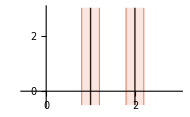

```mathematica
p1=ListLinePlot[Table[{x,y},{x,{(1+(.195)/2+(.205)/2),(1-(.195)/2-(.205)/2),(2+(.195)/2+(.205)/2),(2-(.195)/2-(.205)/2)}},{y,-0.5,3,0.1}],ImageSize->190,PlotStyle->{{cran,Thickness[0.004]}},PlotRange->{{-0.5,3},{-0.5,3}},Epilog->{{Line[{{2,-0.5},{2,3}}]},{Line[{{1,-0.5},{1,3}}]},{Opacity[0.2],cran,Rectangle[{1-(.195)/2-(.205)/2,-0.5},{1+(.195)/2+(.205)/2,3}]},{Opacity[0.2],cran,Rectangle[{2-(.195)/2-(.205)/2,-0.5},{2+(.195)/2+(.205)/2,3}]}}]
```

5.2 Plot of example 1 with potential on both sides equal to z^2.

```mathematica
inc=Flatten[Table[{1+x^2},{x,0.1,√0.5,.1}]];
```

```mathematica
incm=Flatten[Table[{1-x^2},{x,0.1,√0.5,.1}]];
```

```mathematica
incn=Flatten[Table[{2+x^2},{x,0.1,√0.5,.1}]];
```

```mathematica
inco=Flatten[Table[{2-x^2},{x,0.1,√0.5,.1}]];
```

```mathematica
p1=ListLinePlot[Table[{x,y},{x,inc},{y,-0.5,3,0.1}],ImageSize->190,PlotStyle->{{cran,Thickness[0.004]}},PlotRange->{{-0.5,3},{-0.5,3}},Epilog->{{Line[{{2,-0.5},{2,3}}]},{Line[{{1,-0.5},{1,3}}]}}];
```

```mathematica
p2=ListLinePlot[Table[{x,y},{x,incm},{y,-0.5,3,0.1}],ImageSize->190,PlotStyle->{{cran,Thickness[0.004]}},PlotRange->{{-0.5,3},{-0.5,3}}];
p3=ListLinePlot[Table[{x,y},{x,incn},{y,-0.5,3,0.1}],ImageSize->190,PlotStyle->{{cran,Thickness[0.004]}},PlotRange->{{-0.5,3},{-0.5,3}}];
p4=ListLinePlot[Table[{x,y},{x,inco},{y,-0.5,3,0.1}],ImageSize->190,PlotStyle->{{cran,Thickness[0.004]}},PlotRange->{{-0.5,3},{-0.5,3}}];
```

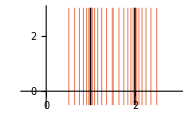

```mathematica
Show[p1,p2,p3,p4]
```

5.3 Plot of example 1 with potential on both sides equal to ⅈ z^2.

If this z were not squared, the ⅈ would have the effect of flipping the Re and Im parts of the points. As it is

```mathematica
Clear["Global`*"]
```

```mathematica
ComplexExpand[ⅈ(x+ⅈ y)^2]
```

-2 x y+ⅈ (x^2-y^2)

It’s a little more complicated than simple flipping. I will suppose that my plates are at x=2 and x=8. Then I can take a look at

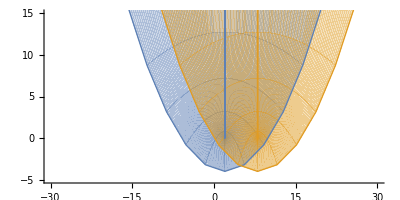

```mathematica
ParametricPlot[{Through[{Re,Im}[(-2 x y+ⅈ (x^2-y^2))+2]],Through[{Re,Im}[(-2 x y+ⅈ (x^2-y^2))+8]]},{x,-25,25},{y,0,2}, PlotRange->{{-30,30},{-5,15}},Frame->False,ImageSize->400]
```

It looks like Mathematica is plotting the poles of the functions in the location where the plates would be. If a plate happens to occupy the space of a pole, I suppose that wouldn’t affect the propagation of the potential field. To be shown right, this plot should show the interaction of the intersecting fields, but that would require way more expertise than I have.

5.4 Plot of example 1 with potential on both sides (both plates) equal to ⅇ^z.

Showing only a handful of possible tracks.

```mathematica
Clear["Global`*"]
```

```mathematica
p1=Plot[{ⅇ^(x-4),ⅇ^(2( x-4)),ⅇ^(3 ( x-4)),ⅇ^(4 ( x-4)),1+ⅇ^(x-4),1+ⅇ^(2( x-4)),1+ⅇ^(3 ( x-4)),1+ⅇ^(4 ( x-4)),2+ⅇ^(x-4),2+ⅇ^(2( x-4)),2+ⅇ^(3 ( x-4)),2+ⅇ^(4 ( x-4)),3+ⅇ^(x-4),3+ⅇ^(2( x-4)),3+ⅇ^(3 ( x-4)),3+ⅇ^(4 ( x-4))},{x,4,8},PlotRange->{{0,10},{0,10}},Epilog->{{Thick,Line[{{4,0},{4,10}}]},{Thick,Line[{{8,0},{8,10}}]},{},}];
```

```mathematica
p2=Plot[{(1/ⅇ)^(x-4),(1/ⅇ)^(2(x-4)),(1/ⅇ)^(3(x-4)),(1/ⅇ)^(4(x-4)),1+(1/ⅇ)^(x-4),1+(1/ⅇ)^(2(x-4)),1+(1/ⅇ)^(3(x-4)),1+(1/ⅇ)^(4(x-4)),2+(1/ⅇ)^(x-4),2+(1/ⅇ)^(2(x-4)),2+(1/ⅇ)^(3(x-4)),2+(1/ⅇ)^(4(x-4)),3+(1/ⅇ)^(x-4),3+(1/ⅇ)^(2(x-4)),3+(1/ⅇ)^(3(x-4)),3+(1/ⅇ)^(4(x-4))},{x,0,4},PlotRange->{{0,10},{0,10}}];
```

```mathematica
p3=Plot[{ⅇ^(x-8),ⅇ^(2( x-8)),ⅇ^(3 ( x-8)),ⅇ^(4 ( x-8)),1+ⅇ^(x-8),1+ⅇ^(2( x-8)),1+ⅇ^(3 ( x-8)),1+ⅇ^(4 ( x-8)),2+ⅇ^(x-8),2+ⅇ^(2( x-8)),2+ⅇ^(3 ( x-8)),2+ⅇ^(4 ( x-8)),3+ⅇ^(x-8),3+ⅇ^(2( x-8)),3+ⅇ^(3 ( x-8)),3+ⅇ^(4 ( x-8))},{x,8,12},PlotRange->{{0,10},{0,10}}];
```

```mathematica
p4=Plot[{(1/ⅇ)^(x-8),(1/ⅇ)^(2(x-8)),(1/ⅇ)^(3(x-8)),(1/ⅇ)^(4(x-8)),1+(1/ⅇ)^(x-8),1+(1/ⅇ)^(2(x-8)),1+(1/ⅇ)^(3(x-8)),1+(1/ⅇ)^(4(x-8)),2+(1/ⅇ)^(x-8),2+(1/ⅇ)^(2(x-8)),2+(1/ⅇ)^(3(x-8)),2+(1/ⅇ)^(4(x-8)),3+(1/ⅇ)^(x-8),3+(1/ⅇ)^(2(x-8)),3+(1/ⅇ)^(3(x-8)),3+(1/ⅇ)^(4(x-8))},{x,4,8},PlotRange->{{0,12},{0,10}}];
```

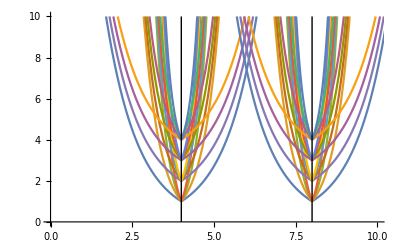

```mathematica
Show[p1,p2,p3,p4]
```

5.5 3D plot of the F[x] = Log[z] function as electrostatic fields around two cylinders in space.

Adapted from Mathematica contour3D documentation. First a look-see at the plot of intervals.

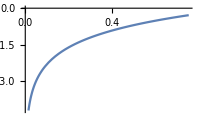

```mathematica
Plot[Log[r],{r,0,0.75},ImageSize->200]
```

Now I have a plot of the log function, but what I need are the y intervals, so

```mathematica
x7=Flatten[Table[N[Solve[Exp[x]==i]],{i,0.01,0.75,0.1}]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{x→-4.60517,x→-2.20727,x→-1.56065,x→-1.17118,x→-0.891598,x→-0.673345,x→-0.494296,x→-0.34249}

And I can use the Log (actually Exp) intervals to inform the Contour3D plot.

```mathematica
ContourPlot3D[Evaluate[electroStaticPotential[{1,-1},{{-1,0,0},{1,0,0}},{x,y,z}]],{x,-5,5},{y,0,4},{z,-4,4},Contours->{-Exp[-0.34],-Exp[-0.49],-Exp[-0.67],-Exp[-0.89],-Exp[-1.17],-Exp[-1.56],-Exp[-2.2],-Exp[-4.6],0,Exp[-4.6],Exp[-2.2],Exp[-1.56],Exp[-1.17],Exp[-0.89],Exp[-0.67],Exp[-0.49],Exp[-0.34]},ContourStyle->Table[Hue[i/7,1,1,0.5],{i,0,6}],Mesh->None,AxesLabel->Automatic]
```

-Graphics3D-

7.  Rectangle, Sin[z]. Let D: 0 ≤ x ≤ π/2, 0 ≤ y ≤ 1; D* the image of D under w = Sin[z]; and Φ*=u^2-v^2. What is the corresponding potential Φ in D? What are its boundary values? Sketch D and D*.

```mathematica
Clear["Global`*"]
```

```mathematica
d2=ImplicitRegion[0≤y≤1&&0≤x≤π/2,{x,y}];
```

```mathematica
oliv=RGBColor[.572,.58,.109];
```

A plot of the z-plane could be helpful.

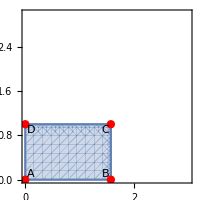

```mathematica
p3=RegionPlot[{x,y}∈d2,{x,0,3},{y,0,3},ImageSize->200,Epilog->{{Red,PointSize[0.03],Point[{0,0}]},{Red,PointSize[0.03],Point[{π/2,0}]},{Red,PointSize[0.03],Point[{π/2,1}]},{Red,PointSize[0.03],Point[{0,1}]},{Text[Style[A,Medium],{0.1,0.1}]},{Text[Style[B,Medium],{π/2-0.1,0.1}]},{Text[Style[C,Medium],{π/2-0.1,0.9}]},{Text[Style[D,Medium],{0.1,0.9}]}}]
```

A plot of the z-plane mapped onto the w-plane by the problem’s designated mapping function is below.

```mathematica
p7=ParametricPlot[Through[{Re,Im}[Sin[(x+ⅈ y)]]],{x,y}∈d2, PlotRange->{{-2,3},{-2,3}},Frame->True,ImageSize->200]
```

-Graphics-

Putting the plots next to each other could make things easier to think about.

```mathematica
p1=ListLinePlot[Table[{Re[Sin[(x+ⅈ y)]],Im[Sin[(x+ⅈ y)]]},{x,0,π/2,0.1},{y,0,1,0.1}],ImageSize->300,PlotStyle->{{oliv,Thickness[0.004]}}];
```

```mathematica
p4=ListLinePlot[Table[Table[{Re[Sin[(x+ⅈ y)]],Im[Sin[(x+ⅈ y)]]},{x,0,1.59,0.0365}],{y,0.1,1.0,0.1}],ImageSize->300,PlotStyle->{{oliv,Thickness[0.004]},{oliv,Thickness[0.004]}}];
```

Here is something strange. Below is a Listplot with one point coordinate commented out. Yet in Mathematica 10.3 the final two mapped points show up simultaneously when the third input coordinate {π/2,1} is exposed. (The order of traverse was verified from the s.m.)

```mathematica
p6=ListPlot[Table[{Re[Sin[(x+ⅈ y)]],Im[Sin[(x+ⅈ y)]]},{x,{0,π/2,π/2(*,0*)}},{y,{0,0,1(*,1*)}}],PlotStyle->{{Black,PointSize[0.02]}},Epilog->{{Text["A",{0.05,0.05}]},{Text["B",{0.95,-0.05}]},{Text["C",{1.59,0.05}]},{Text["D",{0.05,1.22}]}},PlotRange->{{-0.1,1.75},{-0.1,1.3}},ImageSize->350];
```

Trivial comment. It is necessary that the first Show item be p6 for the point labels to show up.

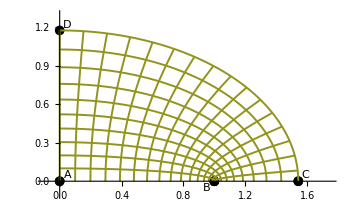
-Graphics--Graphics--Graphics-

```mathematica
Row[{p3,p7,Show[p6,p1,p4]}]
```

Now that I’ve done the plots, maybe I should take care of some math. The problem gives that Φ^* = u^2-v^2. I am prompted to recall that the sine conformal transform is covered on p. 750-751. There talk deals with the w-plane ellipse and provides the equations

```mathematica
u[x_,y_]=Sin[x]Cosh[y]
```

Cosh[y] Sin[x]

and

```mathematica
v[x_,y_]=Cos[x]Sinh[y]
```

Cos[x] Sinh[y]

I am given that in w

```mathematica
SuperStar[Φ][u_,v_]=u[x,y]^2-v[x,y]^2
```

Cosh[y]^2 Sin[x]^2-Cos[x]^2 Sinh[y]^2

and left to ponder how the potential will be distributed along the mapped boundary. I need to consider the corner points

```mathematica
Table[{Cosh[y]^2 Sin[x]^2,-Cos[x]^2 Sinh[y]^2},{x,{0,π/2}},{y,{0,1}}]
```

{{{0,0},{0,-Sinh[1]^2}},{{1,0},{Cosh[1]^2,0}}}

```mathematica
N[-Sinh[1]^2]
```

-1.3811

```mathematica
N[Cosh[1]^2]
```

2.3811

and looking at a grid may help organize

```mathematica
data={{"point A","x=0 y=0",0,0},{"point B","x=π/2 y=0",1,0},{"point C","x=π/2 y=1",2.3811,0},{"point D","x=0 y=1",0,-1.3811}}
```

{{point A,x=0 y=0,0,0},{point B,x=π/2 y=0,1,0},{point C,x=π/2 y=1,2.3811,0},{point D,x=0 y=1,0,-1.3811}}

```mathematica
Text@Grid[Prepend[data,{" "," ","Cosh[y]^2Sin[x]^2","-Cos[x]^2Sinh[y]^2"}],Frame->All]
```

|   | Cosh[y]^2Sin[x]^2 | -Cos[x]^2Sinh[y]^2
point A | x=0 y=0 | 0 | 0
point B | x=π/2 y=0 | 1 | 0
point C | x=π/2 y=1 | 2.3811 | 0
point D | x=0 y=1 | 0 | -1.3811

The functions Φ^* and Φ behave in the same way, which is what the mapping trick is all about. So considering curves (in w) or sides (in z), the potential will equal the sum of the right columns in my grid. I see that for A - B the potential increases from 0 to 1, then on B - C the potential increases from 1 to 2.38, then on C - D the potential decreases from 2.38 to -1.38, then on D - A the potential increases from -1.38 to 0.

9.  Translation. What happens in problem 7 if we replace Sin[z] by Cos[z] = Sin[z+π/2]?

```mathematica
Clear["Global`*"]
```

```mathematica
d2=ImplicitRegion[0≤y≤1&&0≤x≤π/2,{x,y}];
```

```mathematica
p3=RegionPlot[{x,y}∈d2,{x,0,3},{y,0,3},ImageSize->200,Epilog->{{Red,PointSize[0.03],Point[{0,0}]},{Red,PointSize[0.03],Point[{π/2,0}]},{Red,PointSize[0.03],Point[{π/2,1}]},{Red,PointSize[0.03],Point[{0,1}]},{Text[Style[A,Medium],{0.1,0.1}]},{Text[Style[B,Medium],{π/2-0.1,0.1}]},{Text[Style[C,Medium],{π/2-0.1,0.9}]},{Text[Style[D,Medium],{0.1,0.9}]}}]
```

-Graphics-

```mathematica
p7=ParametricPlot[Through[{Re,Im}[Cos[(x+ⅈ y)]]],{x,y}∈d2, PlotRange->{{-2,3},{-2,3}},Frame->True,ImageSize->200]
```

-Graphics-

```mathematica
p1=ListLinePlot[Table[{Re[Cos[(x+ⅈ y)]],Im[Cos[(x+ⅈ y)]]},{x,0,π/2,0.1},{y,0,1,0.1}],ImageSize->300,PlotStyle->{{Blue,Thickness[0.004]}}];
```

```mathematica
p4=ListLinePlot[Table[Table[{Re[Cos[(x+ⅈ y)]],Im[Cos[(x+ⅈ y)]]},{x,0,1.59,0.0365}],{y,0.1,1.0,0.1}],ImageSize->300,PlotStyle->{{Blue,Thickness[0.004]},{Blue,Thickness[0.004]}}];
```

```mathematica
p6=ListPlot[Table[{Re[Cos[(x+ⅈ y)]],Im[Cos[(x+ⅈ y)]]},{x,{0,π/2,π/2(*,0*)}},{y,{0,0,1(*,1*)}}],PlotStyle->{{Black,PointSize[0.02]}},Epilog->{{Text["A",{0.05,0.05}]},{Text["B",{0.95,-0.05}]},{Text["C",{1.59,0.05}]},{Text["D",{0.05,-1.22}]}},PlotRange->{{-0.1,1.75},{0.1,-1.3}},ImageSize->350];
```

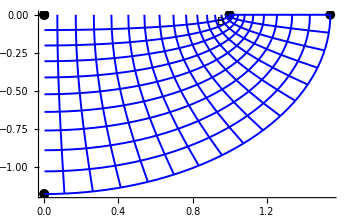
-Graphics--Graphics--Graphics-

```mathematica
Row[{p3,p7,Show[p6,p1,p4]}]
```

Down to this level, I do not see any differences between the Sin and Cos cases, except for the obvious change in quadrant. I expect the assignment of bands of potential would be analogous to the Sin case.

13.  At z = ±1 in figure 405 the tangents to the equipotential lines as shown make equal angles. Why?

The potentials in the two semicircular plates are mirror images, therefore the equipotential curves should be and are drawn as mirror images, thus equal tangent angles. The text answer also mentions conformal attributes, which of course do include preserved angles, but to me it looks like the two semicircular plates in figure 405 are in a pre-mapped state.